```mathematica
erf =({LightGray,Arrowheads[{0,.015}],Arrow[#1,.35]}&);
```

```mathematica
vcr1={{0,0(*Search*)},{2,2 (*Customers*)},{3,.8 (*suppliers*)},{3,-0.8(*Orders*)},{2,-2 (*stock*)}, {5,2 (*MasterDetail*)}};
vrf = ({White, EdgeForm[Blue],Black,
Inset[Style[#2, FontSize -> 14, FontFamily -> "Cambria" ], #1]}&);
```

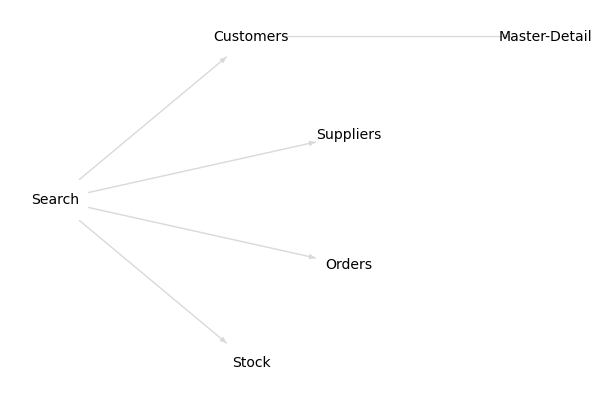

```mathematica
gpSeach=GraphPlot[{search -> customers,search ->  suppliers, search -> orders, search -> stock, customers->masterDetail }, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr1,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{600, 400}]
```

```mathematica
search=Framed[ Style["Search", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Search

```mathematica
?Framed
```

RowBox[{"Framed", "[", StyleBox["expr", "TI"], "]"}] displays a framed version of StyleBox["expr", "TI"].

```mathematica
customers=Framed[ Style["Customers", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Customers

```mathematica
suppliers=Framed[ Style["Suppliers", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Suppliers

```mathematica
orders=Framed[ Style["Orders", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Orders

```mathematica
stock=Framed[ Style["Stock", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Stock

```mathematica
masterDetail=Framed[ Style["Master-Detail", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Master-Detail

```mathematica
addNew=Framed[ Style["Add New", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Add New

```mathematica
details=Framed[ Style["Details", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Details

```mathematica
ordersMasterDetail=Framed[ Style["Orders (Master-Detail)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Orders (Master-Detail)

```mathematica
vrf = ({White, EdgeForm[Blue],Black,
Inset[Style[#2, FontSize -> 14, FontFamily -> "Cambria" ], #1]}&);
```

```mathematica
vcr2={{0,0(*Customers*)},{3,2 (*Add New*)},{3,0 (*Details*)},{3,-2  (*Master*)},{7,-2  (*det_ord*)},{5.5,3.5 (*new*)},{5.5,2(*edit*)},{5.5,0.5(*delete*)}}
```

{{0,0},{3,2},{3,0},{3,-2},{7,-2},{5.5,3.5},{5.5,2},{5.5,0.5}}

```mathematica
Master=Framed[ Style["Master", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Master

```mathematica
DetailOrders=Framed[ Style["Detail (Orders)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Detail (Orders)

```mathematica
newcust =Framed[ Style["New", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

New

```mathematica
editcust =Framed[ Style["Edit", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Edit

```mathematica
delcust =Framed[ Style["Delete", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Delete

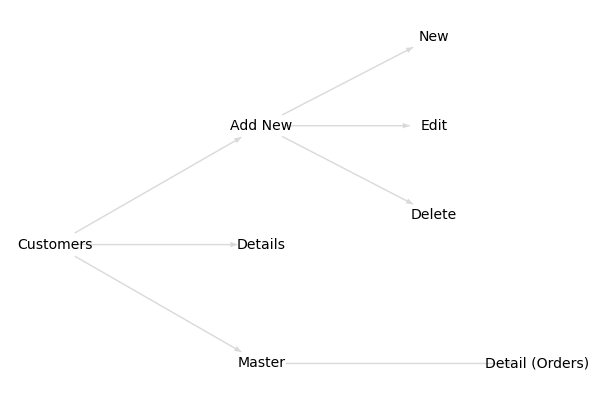

```mathematica
gpCustomers=GraphPlot[{ customers -> addNew, customers -> details, customers -> Master,Master -> DetailOrders, addNew -> newcust,addNew -> editcust,addNew -> delcust}, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr2,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{600, 400}]
```

```mathematica
suppliers
```

Suppliers

```mathematica
stock
```

Stock

```mathematica
adminDAL=Framed[ Style["Admin (DAL)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Admin (DAL)

```mathematica
xmlStock =Framed[ Style["XML", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

XML

```mathematica
generate=Framed[ Style["Generate", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Generate

```mathematica
viewFormatted=Framed[ Style["View Formatted", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

View Formatted

```mathematica
edit=Framed[ Style["Edit", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Edit

```mathematica
editcust,addNew -> delcust
```

```mathematica
currentStockXML=Framed[ Style["CurrentStock.xml", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White, Background -> White]
```

CurrentStock.xml

```mathematica
edit2=Framed[ Style[" Edit ", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Edit

```mathematica
validate=Framed[ Style["Validate?", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Validate?

```mathematica
{2,-2(*XML*)},
{5,0  (*(generate*)},
{6,-2  (*(viewFormatted*)},
{5,-4 (*(edit*)},
{9,-4  (*(currenStockXML*)},
{3,3.5 (*new*)},
{3,2(*edit*)},
{3,0.5(*delete*)}
```

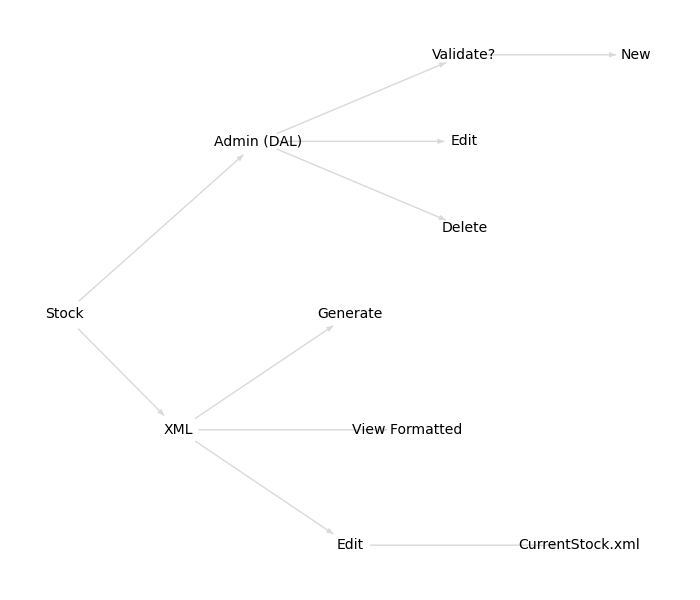

```mathematica
vcr3={
{0,0(*stock*)},
{3.4,3 (*adminDAl*)},
{2,-2(*XML*)},
{5,0  (*(generate*)},
{6,-2  (*(viewFormatted*)},
{5,-4 (*(edit*)},
{9,-4  (*(currenStockXML*)},

{7,4.5(*new*)},

{7,3(*validate*)},
{7,1.5(*delete*)},

{10,4.5(*new*)}




};

gpStock=GraphPlot[
{ stock -> adminDAL, stock -> xmlStock, xmlStock -> generate,xmlStock-> viewFormatted, xmlStock -> edit,edit -> currentStockXML, adminDAL -> validate,adminDAL -> edit2, adminDAL -> delcust,validate-> newcust,
 
}, VertexLabeling -> True, DirectedEdges-> True,VertexLabeling -> True, DirectedEdges-> True,EdgeRenderingFunction->erf,VertexCoordinateRules->vcr3,MultiedgeStyle->1,VertexRenderingFunction-> vrf, ImageSize ->{700, 600}]
```

```mathematica
editcust==edit
```

True

```mathematica
supplerdetails=Framed[ Style["Details (ADO.net)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Details (ADO.net)

```mathematica
newcust
```

New

```mathematica
suppleradmin=Framed[ Style["Admin (DAL)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Admin (DAL)

```mathematica
newSupplierXML =  Framed[ Style["New Supplier (XML)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

New Supplier (XML)

```mathematica
edit
```

Edit

```mathematica
create =  Framed[ Style["Create", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10]
```

Create

```mathematica
adoDetails=Framed[ Style["Details (ADO.net)", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Details (ADO.net)

```mathematica
newSupplierXML=Framed[ Style["New Supplier XML", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

New Supplier XML

```mathematica
editxml2=Framed[ Style["  Edit XML ", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Edit XML

```mathematica
createXML=Framed[ Style["  Create XML ", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

Create XML

```mathematica
supplier=Framed[ Style["Supplier", FontFamily ->  "Verdana", FontSize -> 25],FrameStyle-> Orange, RoundingRadius->5,FrameMargins-> 10, Background -> White]
```

```mathematica
newSupplierXML -> generate, 
newSupplierXML -> viewFormatted, 
newSupplierXML -> edit, 
edit -> currentStockXML,
addNew -> newcust,
addNew -> editcust,addNew -> delcust,
newSupplierXML -> editxml2,
newSupplierXML -> createXML
```

```mathematica
{2,-2(*newSupplierXML*)},
{5,0  (*(generate*)},
{6,-2  (*(viewFormatted*)},
{5,-4 (*(edit*)},
{9,-4  (*(currenStockXML*)};
```

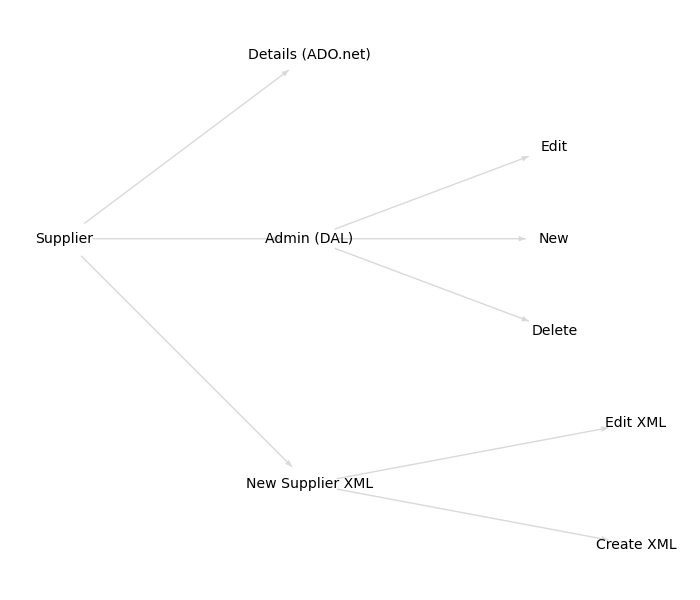

```mathematica
vcr4={
{0,0(*supplier*)},
{3,3 (*adoNet*)},
{3,-4(*newSupplierXML*)},
{3,0(*adminDal*)},
{6,0 (*new*)},
{6,1.5 (*edit*)},
{6,-1.5(*delete*)},
{7,-3(*editXML*)},
{7,-5(*create*)}
};

gpSupp=GraphPlot[
{ supplier -> adoDetails, 
supplier -> newSupplierXML,
supplier -> suppleradmin,
suppleradmin -> newcust,
suppleradmin -> editcust,
suppleradmin -> delcust,
newSupplierXML -> editxml2,
newSupplierXML -> createXML
}, 
VertexLabeling -> True, 
DirectedEdges-> True,
VertexLabeling -> True, 
DirectedEdges-> True,
EdgeRenderingFunction->erf,
VertexCoordinateRules->vcr4,
MultiedgeStyle->1,
VertexRenderingFunction-> vrf, 
ImageSize ->{700, 600}]
```